```mathematica
(*copy pasted from Mathematica stackexchange. TermErsetzung uses user defined variables to simplify expression/eliminate variables from an expression.*)
```

```mathematica
Λ[n] =Λ[n_]:= DiagonalMatrix[Join[{-r1},ConstantArray[-(r1+r2),n-2],{-r2}]]+DiagonalMatrix[ConstantArray[r2,n-1],1]+DiagonalMatrix[ConstantArray[r1,n-1],-1];
```

```mathematica
Λ[3]//MatrixForm
```

(-r1 | r2 | 0
r1 | -r1-r2 | r2
0 | r1 | -r2)

```mathematica
assum= r1>r2 && r2 > 0;
```

```mathematica
sortWithAssumptions[Eigenvalues[Λ[3]],
assum]
```

sortWithAssumptions[{0,-r1-√r1 √r2-r2,-r1+√r1 √r2-r2},r1>r2&&r2>0]

```mathematica
sortWithAssumptions[Eigenvalues[Λ[4]],assum]
```

sortWithAssumptions[{0,-r1-r2,-r1-√2 √r1 √r2-r2,-r1+√2 √r1 √r2-r2},r1>r2&&r2>0]

```mathematica
sortWithAssumptions[Eigenvalues[Λ[5]],assum]
```

sortWithAssumptions[{0,1/2 (-2 r1-2 r2-√2 √(3 r1 r2-√5 r1 r2)),1/2 (-2 r1-2 r2+√2 √(3 r1 r2-√5 r1 r2)),1/2 (-2 r1-2 r2-√2 √(3 r1 r2+√5 r1 r2)),1/2 (-2 r1-2 r2+√2 √(3 r1 r2+√5 r1 r2))},r1>r2&&r2>0]

```mathematica
sortWithAssumptions[Eigenvalues[Λ[10]], assum]
```

sortWithAssumptions[{0,-r1-r2,1/2 (-2 r1-2 r2-√2 √(3 r1 r2-√5 r1 r2)),1/2 (-2 r1-2 r2+√2 √(3 r1 r2-√5 r1 r2)),1/2 (-2 r1-2 r2-√2 √(5 r1 r2-√5 r1 r2)),1/2 (-2 r1-2 r2+√2 √(5 r1 r2-√5 r1 r2)),1/2 (-2 r1-2 r2-√2 √(3 r1 r2+√5 r1 r2)),1/2 (-2 r1-2 r2+√2 √(3 r1 r2+√5 r1 r2)),1/2 (-2 r1-2 r2-√2 √(5 r1 r2+√5 r1 r2)),1/2 (-2 r1-2 r2+√2 √(5 r1 r2+√5 r1 r2))},r1>r2&&r2>0]

```mathematica
Cos[Pi/10]
```

√(5/8+(√5)/8)

```mathematica
Sqrt[6+Sqrt[5]]
```

√(6+√5)

```mathematica
N[sortWithAssumptions[Eigenvalues[Λ[10]],assum]]/. {r1->2, r2->1}
```

sortWithAssumptions[{0.,-3.,-3.87403,-2.12597,-4.66251,-1.33749,-5.28825,-0.711754,-5.68999,-0.310006},True]

```mathematica
Table[N[-1-2-2*Sqrt[2]Cos[k*Pi/10]],{k,1,10}]
```

{-5.68999,-5.28825,-4.66251,-3.87403,-3.,-2.12597,-1.33749,-0.711754,-0.310006,-0.171573}

```mathematica
N[Eigenvectors[Λ[6]]] /. {r1->2, r2->1}
```

{{1/32,1/16,1/8,1/4,1/2,1.},{-0.25,1/4,1/2,-0.5,-1.,1.},{1/4,-0.603553,1/(2 √2),1/(√2),-1.70711,1.},{1/4,0.103553,-0.353553,-0.707107,-0.292893,1.},{-0.25,0.862372,-1.61237,2.22474,-2.22474,1.},{-0.25,-0.362372,-0.387628,-0.224745,0.224745,1.}}

```mathematica
candidateVecs[r1_,r2_,N_,m_]:= Table[Sqrt[(r1/r2)^(i-1)]*Sin[Pi*i*m/N],{i,1,N}];
```

```mathematica
N[candidateVecs[2,1,6,3]]
```

{1.,0.,-2.,0.,4.,0.}

```mathematica
Table[N[-1-2-2*Sqrt[2]Cos[k*Pi/13]],{k,1,13}]
```

{-5.74624,-5.50445,-5.11711,-4.60673,-4.00297,-3.34093,-2.65907,-1.99703,-1.39327,-0.882892,-0.495552,-0.253762,-0.171573}

```mathematica
N[sortWithAssumptions[Eigenvalues[Λ[13]],assum]]/. {r1->2, r2->1}
```

sortWithAssumptions[{0.,-3.34093,-2.65907,-4.00297,-1.99703,-4.60673,-1.39327,-5.11711,-0.882892,-5.50445,-0.495552,-5.74624,-0.253762},True]

```mathematica
Λ[6]//MatrixForm
```

(-r1 | r2 | 0 | 0 | 0 | 0
r1 | -r1-r2 | r2 | 0 | 0 | 0
0 | r1 | -r1-r2 | r2 | 0 | 0
0 | 0 | r1 | -r1-r2 | r2 | 0
0 | 0 | 0 | r1 | -r1-r2 | r2
0 | 0 | 0 | 0 | r1 | -r2)

```mathematica
CharacteristicPolynomial[Λ[6],x]
```

r1^5 x+r1^4 r2 x+r1^3 r2^2 x+r1^2 r2^3 x+r1 r2^4 x+r2^5 x+5 r1^4 x^2+8 r1^3 r2 x^2+9 r1^2 r2^2 x^2+8 r1 r2^3 x^2+5 r2^4 x^2+10 r1^3 x^3+18 r1^2 r2 x^3+18 r1 r2^2 x^3+10 r2^3 x^3+10 r1^2 x^4+16 r1 r2 x^4+10 r2^2 x^4+5 r1 x^5+5 r2 x^5+x^6

```mathematica
toeplitzLambda[n_] := DiagonalMatrix[ConstantArray[-r1-r2,n]]+ DiagonalMatrix[ConstantArray[r2,n-1],1]+ DiagonalMatrix[ConstantArray[r1,n-1],-1]
```

```mathematica
p[x]= CharacteristicPolynomial[toeplitzLambda[6],x]
```

r1^6+r1^5 r2+r1^4 r2^2+r1^3 r2^3+r1^2 r2^4+r1 r2^5+r2^6+6 r1^5 x+10 r1^4 r2 x+12 r1^3 r2^2 x+12 r1^2 r2^3 x+10 r1 r2^4 x+6 r2^5 x+15 r1^4 x^2+30 r1^3 r2 x^2+36 r1^2 r2^2 x^2+30 r1 r2^3 x^2+15 r2^4 x^2+20 r1^3 x^3+40 r1^2 r2 x^3+40 r1 r2^2 x^3+20 r2^3 x^3+15 r1^2 x^4+25 r1 r2 x^4+15 r2^2 x^4+6 r1 x^5+6 r2 x^5+x^6

```mathematica
q[x]=CharacteristicPolynomial[Λ[7],x]
```

-r1^6 x-r1^5 r2 x-r1^4 r2^2 x-r1^3 r2^3 x-r1^2 r2^4 x-r1 r2^5 x-r2^6 x-6 r1^5 x^2-10 r1^4 r2 x^2-12 r1^3 r2^2 x^2-12 r1^2 r2^3 x^2-10 r1 r2^4 x^2-6 r2^5 x^2-15 r1^4 x^3-30 r1^3 r2 x^3-36 r1^2 r2^2 x^3-30 r1 r2^3 x^3-15 r2^4 x^3-20 r1^3 x^4-40 r1^2 r2 x^4-40 r1 r2^2 x^4-20 r2^3 x^4-15 r1^2 x^5-25 r1 r2 x^5-15 r2^2 x^5-6 r1 x^6-6 r2 x^6-x^7

```mathematica
PolynomialRemainder[q[x],p[x],x]
```

0

```mathematica
toeplitzLambda[5]//MatrixForm
```

(-r1-r2 | r2 | 0 | 0 | 0
r1 | -r1-r2 | r2 | 0 | 0
0 | r1 | -r1-r2 | r2 | 0
0 | 0 | r1 | -r1-r2 | r2
0 | 0 | 0 | r1 | -r1-r2)

```mathematica
totalEnt[M_]:=Module[{F =1/M}, F/2*Sum[Exp[-k/2*F]/Sinh[k/2*F],{k,1,M}] ];
```

```mathematica
approximatingIntegral[M_]:=1/2* NIntegrate[Exp[-x/2]/Sinh[x/2],{x,1/M,1}];
```

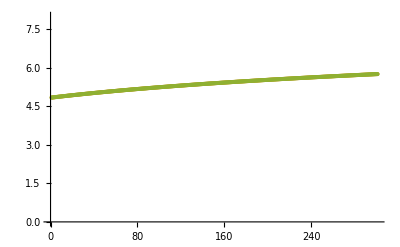

```mathematica
ListPlot[{Table[totalEnt[M,Exp[-1]],{M,200,500}],Table[approximatingIntegral[M],{M,200,500}], Table[Log[(1-Exp[-1])/(1-Exp[-1/M])],{M,200,500}]},PlotRange->{Automatic,{0,8}}]
```

```mathematica
totalEnt[10,0.1]
```

totalEnt[10,0.1]

```mathematica
totalEnt[12,0.1]
```

totalEnt[12,0.1]

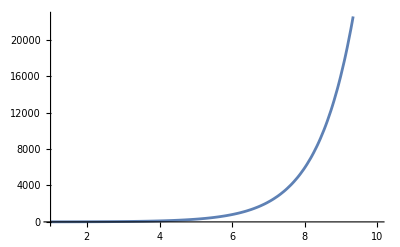

```mathematica
Plot[(Exp[3/2*x]-1/2*Exp[x/2])/Sinh[x/2],{x,1,10}]
```

```mathematica
Sum[j*x^j, {j,0,N-1}]//FullSimplify
```

(x+(N (-1+x)-x) x^N)/(-1+x)^2

```mathematica
N[Exp[7]]
```

1096.63

Below  I’m doing some analysis to observe the scaling with M and N, setting δ = 1/e^3 ~ 0.05 for simplicity. I use n in place of N because Mathematica has a built in function called N.

```mathematica
(*piN is the probability mass in the n-th state after k steps*)
```

```mathematica
rateRatio[M_,c_,k_]:= Exp[-c*k/M];
```

```mathematica
adjacentDistsKLD[n_,M_,c_,k_]:=If[k !=0,c/M*(rateRatio[M,c,k]-n*rateRatio[M,c,k]^n+(n-1)*rateRatio[M,c,k]^(n+1))/((1-rateRatio[M,c,k])(1-rateRatio[M,c,k]^n)),c*(n-1)/(2*M)];
```

```mathematica
totalEntProd[n_,M_,c_]:=-(n-1)*c+Sum[adjacentDistsKLD[n,M,c,k],{k,-M,M}];
```

```mathematica
N[totalEntProd[10,22,3]]
```

0.613636

```mathematica
cfTotalEntProd[10,22,3]
```

0.613636

```mathematica
p1=ListPlot[Table[N[totalEntProd[10,m]],{m,5,200}]];
```

```mathematica
p2= Plot[0.12, {x,0,200},PlotStyle->Red];
```

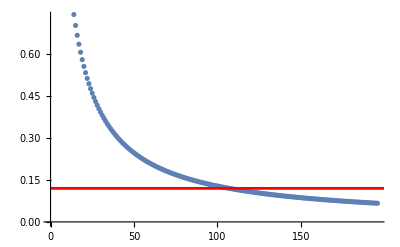

```mathematica
Show[p1,p2]
```

How  does  the  entropy  production  scale  with  M  for  N = 2?

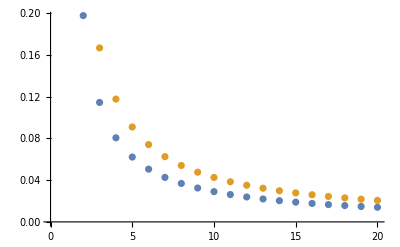

```mathematica
ListPlot[{Table[totalEntProd[2, m],{m,2,100, 5}], Table[2/m,{m,2,100,5}] }]
```

How  does  EP  scale  with  N  if  we  allow  M = 10  buffer  states  per  computational  state?

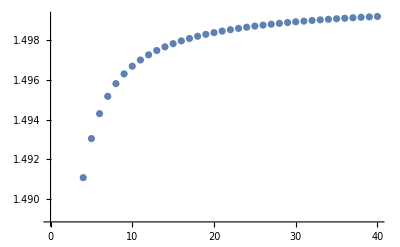

```mathematica
ListPlot[Table[cTotalEntProd[n, (n-1)],{n,2,200, 5}]]
```

This  looks logorithmic or bounded...

```mathematica
linearBufferScaling1 = Table[{n,cTotalEntProd[n, (n-1)] }, {n,2,200,5}];
```

```mathematica
linearBufferScaling10 = Table[{n,cTotalEntProd[n, 10*(n-1)] }, {n,2,200,5}];
```

```mathematica
linearBufferScaling20 =  Table[{n,cTotalEntProd[n, 20*(n-1)] }, {n,2,200,5}];
```

```mathematica
linearBufferScaling30 =  Table[{n,cTotalEntProd[n, 30*(n-1)] }, {n,2,200,5}];
```

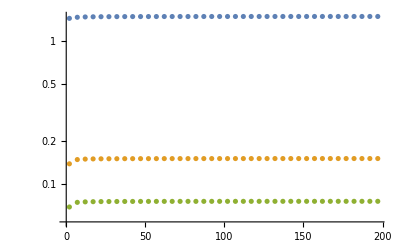

```mathematica
ListLogPlot[{linearBufferScaling1, linearBufferScaling10, linearBufferScaling20}]
```

```mathematica
Log[1.2]/0.148
```

1.2319

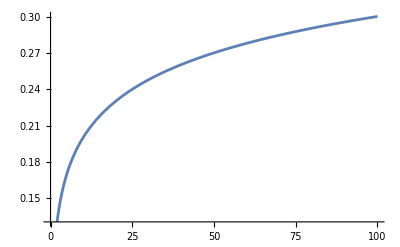

```mathematica
Plot[Log[10*x]/23,{x,2,100}, PlotRange->Automatic]
```

```mathematica
linearBufferScaling
```

{{2,0.137632},{7,0.147448},{12,0.148591},{17,0.149027},{22,0.149257},{27,0.149399},{32,0.149496},{37,0.149565},{42,0.149618},{47,0.149659},{52,0.149693},{57,0.14972},{62,0.149743},{67,0.149762},{72,0.149779},{77,0.149794},{82,0.149806},{87,0.149818},{92,0.149828},{97,0.149837}}

```mathematica
0.149257-0.149806
```

-0.000549

```mathematica
-0.000549/Log[22/82]
```

0.000417276

```mathematica
Integrate[(Exp[-c*x]+(n/5-1)*Exp[-(n+1)*c*x]-n/5*Exp[-n*c*x])/((1-Exp[-c*x])*(1-Exp[-n*c*x])),{x,-1,1},Assumptions->n>0&& c>0]
```

Integrate::idiv: Integral of (-5+5 ⅇ^(c n x)+n-ⅇ^(c x) n)/(5 (-1+ⅇ^(c x)) (-1+ⅇ^(c n x))) does not converge on {-1,1}.

Integrate[(ⅇ^(-c x)+ⅇ^(c (-1-n) x) (-1+n/5)-1/5 ⅇ^(-c n x) n)/((1-ⅇ^(-c x)) (1-ⅇ^(-c n x))),{x,-1,1},Assumptions→n>0&&c>0]

```mathematica
Series[(Exp[-c*x]+(n-1)*Exp[-(n+1)*c*x]-n*Exp[-n*c*x])/((1-Exp[-c*x])*(1-Exp[-n*c*x]))-1/2(n-1),{x,0,5}]
```

-1/12 (c (-1+n^2)) x+1/720 (-c^3+c^3 n^4) x^3+((c^5-c^5 n^6) x^5)/30240+O[x]^6

```mathematica
NSolve[1-Exp[-3]==(1-x)/(1-x^12)]
```

{{x→-0.968371-0.283076 ⅈ},{x→-0.968371+0.283076 ⅈ},{x→-0.662354-0.759354 ⅈ},{x→-0.662354+0.759354 ⅈ},{x→-0.147481-0.994547 ⅈ},{x→-0.147481+0.994547 ⅈ},{x→0.412775-0.91398 ⅈ},{x→0.412775+0.91398 ⅈ},{x→0.840537-0.543227 ⅈ},{x→0.840537+0.543227 ⅈ},{x→0.0497871}}

```mathematica
Log[0.04978]
```

-3.00014

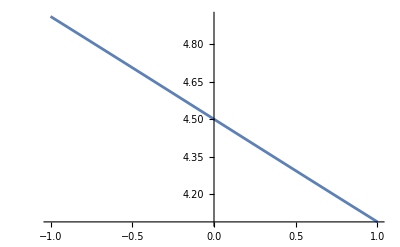

```mathematica
Plot[(Exp[-c*x]+(n-1)*Exp[-(n+1)*c*x]-n*Exp[-n*c*x])/((1-Exp[-c*x])*(1-Exp[-n*c*x]))/. n->10 /. c->0.05,{x,-1,1}]
```

```mathematica
linearBufferScaling10
```

```mathematica
(*another version of EP functions for numerical evaluation*)
```

```mathematica
NrateRatio[M_,k_]:= N[Exp[-3*k/M]];
```

```mathematica
NpiN[n_,M_,k_] := If[k!=0, (1-NrateRatio[M,k])/(1-NrateRatio[M,k]^n), 1/n];
```

```mathematica
NadjacentDistsKLD[n_,M_,k_]:=-Log[NpiN[n,M,k+1]/NpiN[n,M,k]]+If[k !=0,3/M*(NrateRatio[M,k]-n*NrateRatio[M,k]^n+(n-1)*NrateRatio[M,k]^(n+1))/((1-NrateRatio[M,k])(1-NrateRatio[M,k]^n)),3*(n-1)/(2*M)];
```

```mathematica
NtotalEntProd[n_,M_]:=Sum[NadjacentDistsKLD[n,M,k],{k,-M,M}];
```

```mathematica
EntropySum[n_,M_] := NSum[If[k !=0,3/M*(NrateRatio[M,k]-n*NrateRatio[M,k]^n+(n-1)*NrateRatio[M,k]^(n+1))/((1-NrateRatio[M,k])(1-NrateRatio[M,k]^n)),3*(n-1)/(2*M)], {k,-M,M}]
```

```mathematica
EntropySum[10,20]
```

27.3915

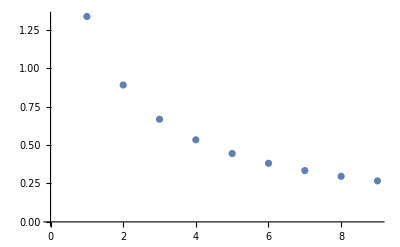

```mathematica
ListPlot[Table[NtotalEntProd[10,M],{M,10,50,5}]]
```

```mathematica
EntropySum[10,50]
```

NumericalMath`NSequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

-181.183

```mathematica
NtotalEntProd[5,40]
```

0.146221

```mathematica
logSum [n_,M_]:= NSum[-Log[NpiN[n,M,k+1]/NpiN[n,M,k]],{k,-M,M}];
```

NumericalMath`NSequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

General::stop: Further output of NumericalMath`NSequenceLimit::seqlim will be suppressed during this calculation.

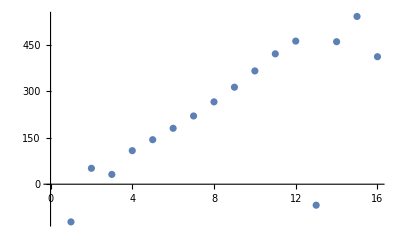

```mathematica
ListPlot[Table[logSum[n,10*n],{n,5,20}]]
```

```mathematica
phi[n_,c_,x_]:= If[x!=0,(Exp[-c*x]-n*Exp[-n*c*x]+(n-1)*Exp[-(n+1)*c*x])/((1-Exp[-c*x])*(1-Exp[-n*c*x])), 1/2*(n-1)];
```

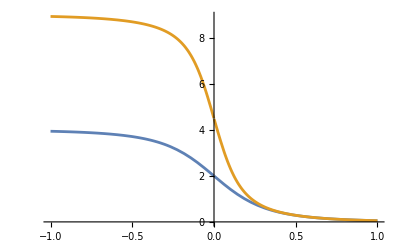

```mathematica
Plot[{phi[5,3,x],phi[10,3,x]},{x,-1,1}]
```

```mathematica
exp[n_,c_,x_]:= Exp[-c*x];
```

```mathematica
Composition[ phi,exp][5,3,1/2]
```

phi[1/ⅇ^(3/2)]

```mathematica
phiPrime[n_,c_,x_] = Derivative[0,0,1][phi][n,c,x]
```

If[x≠0,-(((Exp[-c x]-n Exp[-n c x]+(n-1) Exp[-(n+1) c x]) (ⅇ^(-n c x) n c (1-Exp[-c x])+c Exp[-c x] (1-Exp[-n c x])))/((1-Exp[-c x]) (1-Exp[-n c x]))^2)+((n-1) ⅇ^((-1-n) c x) (-1-n) c+ⅇ^(-n c x) n^2 c-c Exp[-c x])/((1-Exp[-c x]) (1-Exp[-n c x])),0]

```mathematica
FindMaximum[phiPrime[n,c,x],x]
```

FindMaximum::nrnum: The function value (c ⅇ^(-1. c) (ⅇ^(-1. c)+ⅇ^(1. c (-1+Times[«2»])) (-1+n)-ⅇ^(-1. c n) n))/((1-ⅇ^(-1. c))^2 (1-ⅇ^(-1. c n)))+(c ⅇ^(-1. c n) n (ⅇ^(-1. c)+ⅇ^(1. c (-1+Times[«2»])) (-1+n)-ⅇ^(-1. c n) n))/((1-ⅇ^(-1. c)) (1-ⅇ^(-1. c n))^2)-(-c ⅇ^(-1. c)+c ⅇ^(1. c (-1+Times[«2»])) (-1-n) (-1+n)+c ⅇ^(-1. c n) n^2)/((1-ⅇ^(-1. c)) (1-ⅇ^(-1. c n))) is not a real number at {x} = {1.}.

FindMaximum[phiPrime[n,c,x],x]

```mathematica
Limit[phiPrime[n,c,x],x->0]
```

1/12 (c-c n^2)

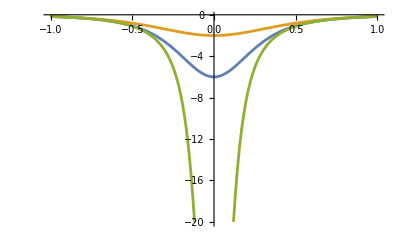

```mathematica
Plot[{phiPrime[5,3,x],phiPrime[3,3,x],phiPrime[15,3,x]},{x,-1,1}, PlotRange->{Automatic,{0,-20}}]
```

```mathematica
phiPrimePrime[n_,c_,x_] = Derivative[0,0,2][phi][n,c,x];
```

```mathematica
Limit[phiPrimePrime[n,c,x],x->0]
```

0

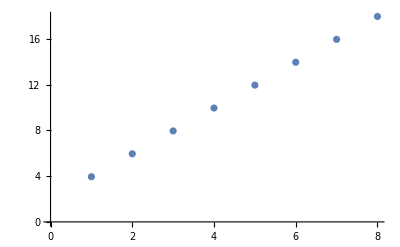

```mathematica
ListPlot[Table[phi[n,3,-1],{n,5,20,2}]]
```

```mathematica
phi[n,c,-1]
```

(ⅇ^c+ⅇ^(-c (-1-n)) (-1+n)-ⅇ^(c n) n)/((1-ⅇ^c) (1-ⅇ^(c n)))

```mathematica
ls1= Table[{n,phi[n,1,1]},{n,5,20,2}];
```

```mathematica
ls2= Table[{n,Exp[-1]/(1-Exp[-1])},{n,5,20,2}];
```

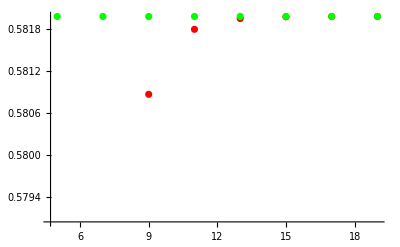

```mathematica
ListPlot[{ls1,ls2},PlotStyle->{Red, Green}]
```

```mathematica
N[Table[{n,phi[n,1,1]-Exp[-1]/(1-Exp[-1])},{n,5,20,2}]]
```

{{5.,-0.0339183},{7.,-0.006389},{9.,-0.00111083},{11.,-0.000183722},{13.,-0.0000293843},{15.,-4.58854×10^-6},{17.,-7.03789×10^-7},{19.,-1.06453×10^-7}}

```mathematica
totalEnts = Table[{m,cfTotalEntProd[10, m,3]/3}, {m,5,20,2}]
```

{{5,0.9},{7,0.642857},{9,0.5},{11,0.409091},{13,0.346154},{15,0.3},{17,0.264706},{19,0.236842}}

```mathematica
integralErrs = Table[{m, 1/m*(phi[10,3,-1]-phi[10,3,1])},{m,5,20,2}];
```

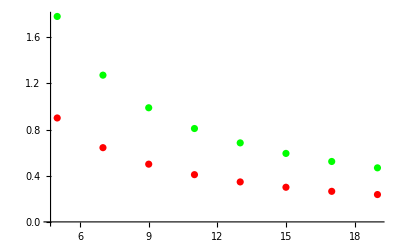

```mathematica
ListPlot[{totalEnts, integralErrs}, PlotStyle->{Red, Green}]
```

```mathematica
Limit[phi[n,c,x],x->0]
```

1/2 (-1+n)

```mathematica
totalEntsLinScale = Table[{α,cfTotalEntProd[10, 10*α,3]/3}, {α,5,20,2}];
```

```mathematica
boundsLinScale = Table[{α, 1/(α*10)*(phi[10,3,-1]-phi[10,3,1])},{α,5,20,2}];
```

```mathematica
approximateBoundsLinScale = Table[{α,1/α-Exp[-3]/(1-Exp[-3])}, {α,5,20,2}];
```

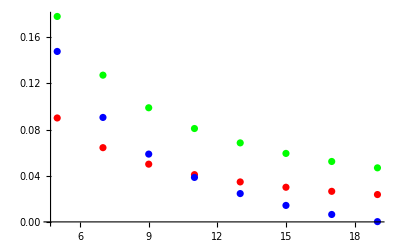

```mathematica
ListPlot[{totalEntsLinScale, boundsLinScale, approximateBoundsLinScale},PlotStyle->{Red, Green, Blue}]
```

```mathematica
totalEntLinScale= Table[{n,cfTotalEntProd[n,5n,2]/2}, {n,5,30,2}]
```

{{5,0.08},{7,0.0857143},{9,0.0888889},{11,0.0909091},{13,0.0923077},{15,0.0933333},{17,0.0941176},{19,0.0947368},{21,0.0952381},{23,0.0956522},{25,0.096},{27,0.0962963},{29,0.0965517}}

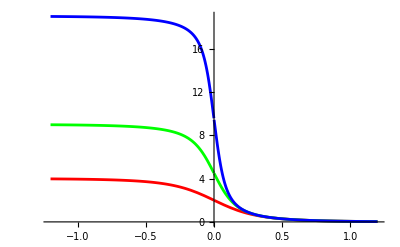

```mathematica
Plot[{phi[5,3,x],phi[10,3,x], phi[20,3,x]},{x,-1.2,1.2},PlotStyle->{Red,Green,Blue}]
```

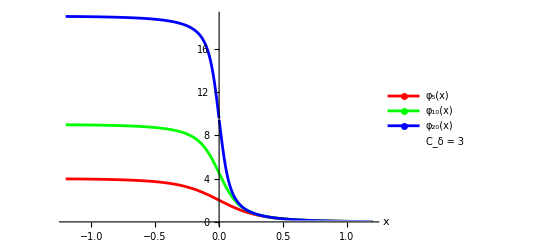

```mathematica
Plot[{phi[5,3,x],phi[10,3,x],phi[20,3,x],0 (*dummy curve for legend*)},{x,-1.2,1.2},PlotStyle->{Red,Green,Blue,White},PlotLegends->Placed[LineLegend[{Style[Subscript[φ,5][x],Italic],Style[Subscript[φ,10][x],Italic],Style[Subscript[φ,20][x],Italic],Style[Row[{Subscript["C","δ"]," = 3"}],Italic]},LegendMarkers->""],{Right,Center}], AxesLabel->Automatic, LabelStyle->Directive[Bold, Black]]
```

```mathematica
bound[n_,M_,c_] = 1/M*(phi[n,c,-1]-phi[n,c,1]);
```

```mathematica
bound2[n_,M_,c_]= 1/M*(phi[n,c,-1]-phi[n,c,0]);
```

```mathematica
EntprodNForPlot= Table[{n,cfTotalEntProd[n,10,3]/3},{n,5,30,2}];
```

```mathematica
EntprodMForPlot= Table[{m,cfTotalEntProd[10,m,3]/3},{m,5,30,2}];
```

```mathematica
boundM = Table[{m,bound[10,m,3]},{m,5,30,2}];
```

```mathematica
boundN = Table[{n,bound[n,10,3]},{n,5,30,2}];
```

```mathematica
bound2M = Table[{m,bound2[10,m,3]},{m,5,30,2}];
```

```mathematica
bound2N =Plot[bound2[n,10, 3],{n,5,30},PlotStyle->Blue];
```

```mathematica
lsPlot = ListPlot[{EntprodNForPlot,boundN}, PlotStyle->{Red, Green}];
```

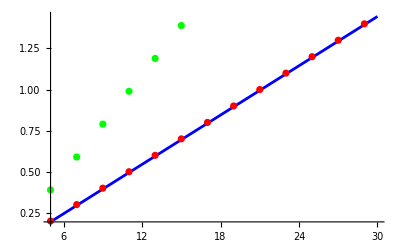

```mathematica
Show[bound2N, lsPlot]
```

```mathematica
boundN/EntprodNForPlot
```

{{1,1.94761},{1,1.96507},{1,1.9738},{1,1.97904},{1,1.98253},{1,1.98503},{1,1.9869},{1,1.98836},{1,1.98952},{1,1.99047},{1,1.99127},{1,1.99194},{1,1.99251}}

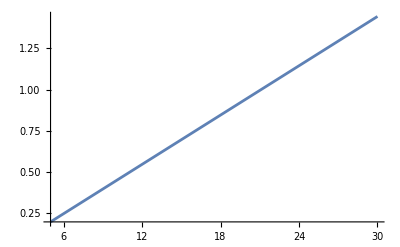

```mathematica
Plot[bound[10,n,3]/2,{n,5,30}]
```

```mathematica
cfTotalEntProd[10,10,3]/3-bound[10,10,3]/2
```

0.00523957

```mathematica
phiCentered[n_,c_,x_] := phi[n,c,x]-phi[n,c,0];
```

```mathematica
phiCentered[n,c,x]+phiCentered[n,c,-x]//FullSimplify
```

0

```mathematica
Factor[x^(n+1)-x^n-x-1]
```

-1-x-x^n+x^(1+n)

```mathematica
totalEntsLinScale2 = Table[{n,cfTotalEntProd[n, 2n,3]}, {n,5,30,2}];
```

```mathematica
totalEntsLinScale3 = Table[{n,cfTotalEntProd[n, 3n,3]}, {n,5,30,2}];
```

```mathematica
totalEntsLinScale5= Table[{n,cfTotalEntProd[n, 5*n,3]}, {n,5,30,2}];
```

```mathematica
lims = Plot[{3/4,3/6,3/10},{x,5,30}, PlotStyle->{Directive[Blue,Dashed], Directive[Red, Dashed], Directive[Green, Dashed]},PlotRange->{Automatic,{0,0.8}}];
```

```mathematica
ents = ListPlot[{totalEntsLinScale2, totalEntsLinScale3, totalEntsLinScale5}, PlotStyle->{Directive[Blue,Dashed], Directive[Red], Directive[Green, Dashed]}, PlotRange->{Automatic, {0,0.8}}];
```

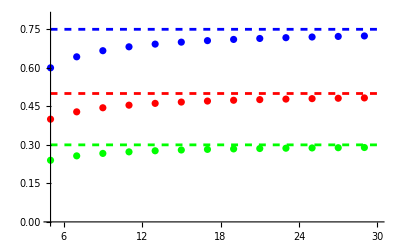

```mathematica
Show[lims, ents]
```

```mathematica
lims=Plot[{3/4,3/6,3/10},{x,5,30},PlotStyle->{Directive[Blue,Dashed],Directive[Red,Dashed],Directive[Green,Dashed]},PlotRange->{Automatic,{0,0.8}},PlotLegends->None,AxesLabel->{"N",Subscript["Σ","tot"]},LabelStyle->Directive[Bold, Black]];

ents=ListPlot[{totalEntsLinScale2,totalEntsLinScale3,totalEntsLinScale5, {1,1}(*dummy point*)},PlotStyle->{Directive[Blue,Dashed],Directive[Red],Directive[Green,Dashed],White (*dummy*)},PlotRange->{Automatic,{0,0.8}},PlotLegends->Placed[LineLegend[{Style[Row[{"α = 2"}],Italic],Style[Row[{"α = 3"}],Italic],Style[Row[{"α = 5"}],Italic],Style[Row[{Subscript["C","δ"]," = 3"}],Italic]},LegendMarkers->"---"],{1, 0.5}], AxesLabel->{"N",Subscript["Σ","tot"]}, LabelStyle->Directive[Bold, Black]];

Show[lims,ents]
```

-Graphics-